```mathematica
4*m*v/(e*B)
```

48972.2

```mathematica
50000/32.3
```

```mathematica
1547.9876160990714
```

{{y[t]→12.5 Cos[0.000932517 t]+17.3187 Sin[0.000932517 t],x[t]→25000.+32.2835 t}}

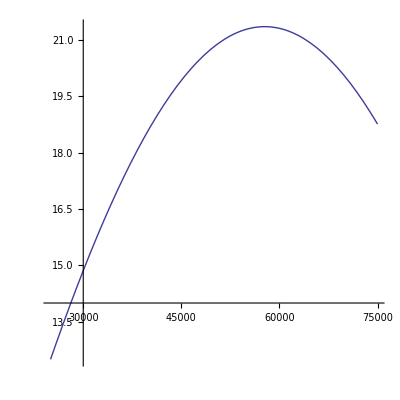

```mathematica
sol=DSolve[{y''[t]==A*y[t],y'[0]==32.3*Sin[.0005],y[0]==25000Sin[.0005],x''[t]==0,x[0]==25000,x'[0]==32.283511},{y[t],x[t]},t]
ParametricPlot[{x[t],y[t]}/.sol,{t,0,1548},AspectRatio-> 1]
```

```mathematica
orig=E0/(v+(B/4+E0/v)*e*dy/m)
```

-(2.4225×10^-13)/(32.3-0.000659558 dy)

```mathematica
Series[E0/(v+(B/4+E0/v)*e*dy/m),{dy,0,1}]
```

-7.5×10^-15-1.53148×10^-19 dy+O[dy]^2

```mathematica
E0/v
```

```mathematica
approx=-7.500000000000001*^-15-1.5314804124482102*^-19 dy
```

-7.5×10^-15-1.53148×10^-19 dy

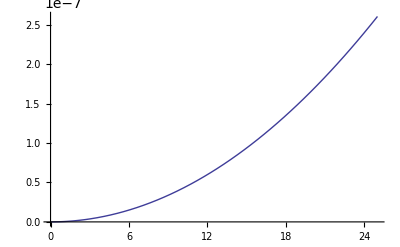

```mathematica
Plot[(orig-approx)/orig,{dy,0,25}]
```

```mathematica
dtot=100000
dw = 50000
B=1.5*10^-14
v=32.3
E0=-(dtot*B*v)/(dw*4)
e=1.60217646*10^-19
m=9.10938188*10^-31
```

100000

50000

1.5×10^-14

32.3

-2.4225×10^-13

1.60218×10^-19

9.10938×10^-31

```mathematica
32.3
```

32.3

```mathematica
β=(e (4 E0^2+B E0 v))/(4 (m v^3))
```

1.53148×10^-19

```mathematica
A=-e*32.283511 *β/m
```

-8.69588×10^-7

```mathematica
Sqrt[8.694602101195509*^-7]
```

0.000932449

```mathematica
0.0009324485026635793/2Pi
```

```mathematica
1/0.0014646866829093517
```

```mathematica
682.7398730858054*v
```

22189.

```mathematica
v/(Sqrt[-A]/(2 Pi))
```

218997.

```mathematica
4*m*v/(e*B)
```

48972.2